## Chladni Patterns

By adjusting a plate on a vibrating source and scatter some dust on it, we can see patterns.

http://en.wikipedia.org/wiki/Ernst_Chladni

### Mathematics

A rigrous way to solve the problem is to set up the equations: 2D vibration and boundary condition at the center of the plate.

However we can know that the result on the plate is just the coordinates of adjoints of standing wave (approximately).

#### Plates

that is, the solutions of

Cos[n Pi x/L] Cos[m Pi y/L]-Cos[m Pi x/L] Cos[n Pi y/L]==0

```mathematica
pEq[m_,n_,L_,x_,y_]:=Cos[n Pi x/L] Cos[m Pi y/L]-Cos[m Pi x/L] Cos[n Pi y/L]==0
```

```mathematica
pEq[1,2,1,x,y]
```

Cos[2 π x] Cos[π y]-Cos[π x] Cos[2 π y]==0

```mathematica
res[m0_,n0_,L0_]:=Block[{m=m0,n=n0,L=L0},sol=Solve[Cos[n Pi x/L] Cos[m Pi y/L]-Cos[m Pi x/L] Cos[n Pi y/L]==0,y]//Quiet;
len=Length[sol];
Show[{Table[Plot[y/.sol[[i]],{x,-1,1}],{i,1,len}]}]
]
```

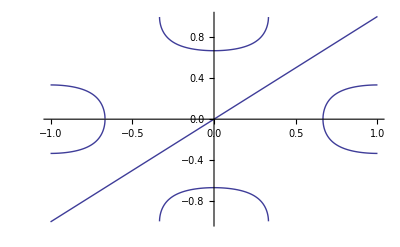

```mathematica
res[2,1,1]
```